```mathematica
point={1,2}
```

{1,2}

```mathematica
N@RotationMatrix[30Degree].point
```

{-0.133975,2.23205}

```mathematica
points={{1, 1, -1, -1}, {2, -2, -2, 2}}
```

{{1,1,-1,-1},{2,-2,-2,2}}

```mathematica
rotated=N[RotationMatrix[30Degree].points]
```

{{-0.133975,1.86603,0.133975,-1.86603},{2.23205,-1.23205,-2.23205,1.23205}}

```mathematica
MatrixForm[{{-0.1339745962155614,1.8660254037844386,-1.8660254037844386,0.1339745962155614},{2.232050807568877,-1.2320508075688772,1.2320508075688772,-2.232050807568877}}]
```

(-0.133975 | 1.86603 | -1.86603 | 0.133975
2.23205 | -1.23205 | 1.23205 | -2.23205)

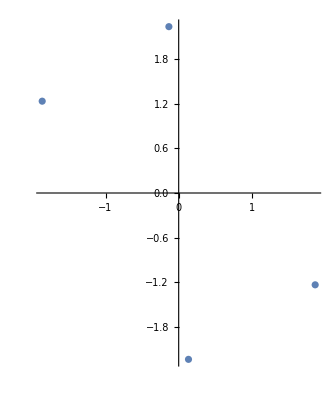

```mathematica
ListPlot[Transpose[rotated],AspectRatio->Automatic]
```

```mathematica
unrotated=RotationMatrix[-30Degree].rotated
```

{{1.,1.,-1.,-1.},{2.,-2.,-2.,2.}}

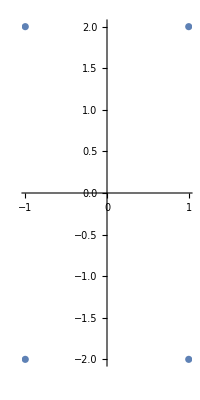

```mathematica
ListPlot[Transpose[unrotated],AspectRatio->Automatic]
```

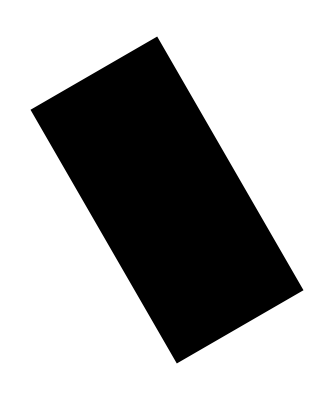

```mathematica
Graphics[Polygon[Transpose[rotated]]]
```

```mathematica
Animate[
data=RotationMatrix[a].points;
Graphics[Polygon[Transpose[data]],Axes->True,PlotRange->{{-2.5,2.5},{-2.5,2.5}}],{a,-Pi,2Pi}]
```

```mathematica
Transpose[data]
```

{{2.22133,-0.256274},{-1.53782,-1.6233},{-2.22133,0.256274},{1.53782,1.6233}}

```mathematica
MatrixForm[{{2.221333800965272,-0.2562735739189247},{-1.5378191397143028,-1.6233028964208627},{-2.221333800965272,0.2562735739189247},{1.5378191397143028,1.6233028964208627}}]
```

(2.22133 | -0.256274
-1.53782 | -1.6233
-2.22133 | 0.256274
1.53782 | 1.6233)

```mathematica
r=RotationMatrix[θ]
```

{{(√3)/2,-1/2},{1/2,(√3)/2}}

```mathematica
s={{2, 0}, {0, 1/3}}
```

{{2,0},{0,1/3}}

```mathematica
Inverse[s]
```

{{1/2,0},{0,3}}

```mathematica
θ=30Degree
```

30 °

```mathematica
q1=s.r.points
```

{{-2+√3,2+√3,2-√3,-2-√3},{1/6+1/(√3),1/6-1/(√3),-1/6-1/(√3),-1/6+1/(√3)}}

```mathematica
{{2 Cos[θ]-4 Sin[θ],2 Cos[θ]+4 Sin[θ],-2 Cos[θ]+4 Sin[θ],-2 Cos[θ]-4 Sin[θ]},{(2 Cos[θ])/3+Sin[θ]/3,-(2 Cos[θ])/3+Sin[θ]/3,-(2 Cos[θ])/3-Sin[θ]/3,(2 Cos[θ])/3-Sin[θ]/3}}
```

{{-2+√3,2+√3,2-√3,-2-√3},{1/6+1/(√3),1/6-1/(√3),-1/6-1/(√3),-1/6+1/(√3)}}

```mathematica
FullSimplify[Inverse[r].Inverse[s].q1]
```

{{1,1,-1,-1},{2,-2,-2,2}}

```mathematica
q2=r.s.points
```

{{-1/3+√3,1/3+√3,1/3-√3,-1/3-√3},{1+1/(√3),1-1/(√3),-1-1/(√3),-1+1/(√3)}}

```mathematica
{{2 Cos[θ]-(2 Sin[θ])/3,2 Cos[θ]+(2 Sin[θ])/3,-2 Cos[θ]+(2 Sin[θ])/3,-2 Cos[θ]-(2 Sin[θ])/3},{(2 Cos[θ])/3+2 Sin[θ],-(2 Cos[θ])/3+2 Sin[θ],-(2 Cos[θ])/3-2 Sin[θ],(2 Cos[θ])/3-2 Sin[θ]}}
```

{{-1/3+√3,1/3+√3,1/3-√3,-1/3-√3},{1+1/(√3),1-1/(√3),-1-1/(√3),-1+1/(√3)}}

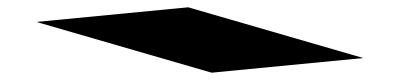

```mathematica
Graphics[Polygon[Transpose[q1]]]
```

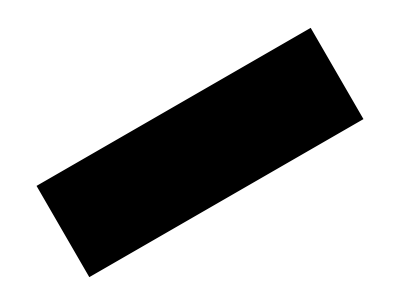

```mathematica
Graphics[Polygon[Transpose[q2]]]
```

```mathematica
points2=Join[points,{{1,1,1,1}}]
```

{{1,1,-1,-1},{2,-2,-2,2},{1,1,1,1}}

```mathematica
T={{1, 0, 2}, {0, 1, 3}, {0, 0, 1}}
```

{{1,0,2},{0,1,3},{0,0,1}}

```mathematica
q=Transpose[T.points2]
```

{{3,5,1},{3,1,1},{1,1,1},{1,5,1}}

```mathematica
data1=q[[All,1;;2]]
```

{{3,5},{3,1},{1,1},{1,5}}

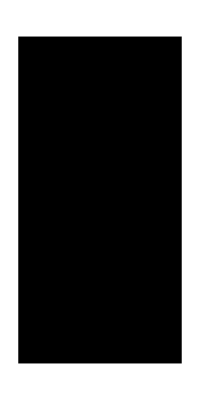

```mathematica
Graphics[Polygon[data1]]
```

```mathematica
Clear[θ]
```

```mathematica
r=RotationMatrix[θ]
```

{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}

```mathematica
s
```

{{2,0},{0,1/3}}

```mathematica
T
```

```mathematica
{{1,0,2},{0,1,3},{0,0,1}}
```

{{1,0,2},{0,1,3},{0,0,1}}

```mathematica
Animate[
r=({{Cos[θ], Sin[θ], 0}, {-Sin[θ], Cos[θ], 0}, {0, 0, 1}});
s=({{Cos[θ], 0, 0}, {0, Sin[θ], 0}, {0, 0, 1}});
T={{1, 0, θ}, {0, 1, θ}, {0, 0, 1}};
data=s.r.T.points2;
Graphics[Polygon[Transpose[data[[{1,2},All]]]],Axes->True,PlotRange->{{-10,10},{-10,10}}],{θ,0,2Pi}]
```

```mathematica
r=({{Cos[θ], Sin[θ], 0}, {-Sin[θ], Cos[θ], 0}, {0, 0, 1}});
s=({{Sin[θ], 0, 0}, {0, Sin[θ], 0}, {0, 0, 1}});
T={{1, 0, θ}, {0, 1, θ}, {0, 0, 1}};
data=T.s.r.points2;
```

```mathematica
Transpose[data[[{1,2},All]]]
```

{{1.37126,1.10808},{0.461428,-0.568686},{-0.376953,-0.11377},{0.532879,1.56299}}

```mathematica
MatrixForm[{{1.3712604704744322,1.108077041244183},{0.4614282194897367,-0.5686859947889067},{-0.3769532985268081,-0.11376986929655891},{0.5328789524578874,1.5629931667365309}}]
```

(1.37126 | 1.10808
0.461428 | -0.568686
-0.376953 | -0.11377
0.532879 | 1.56299)